# Analysing FST output from xerxes

## Loading data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/stephan_schiffels/dev/comp_human_adna_book/fst_working

```mathematica
rawdat=Import["fstat_world_output.tsv"];
```

```mathematica
rawdat[[;;10]]//TableForm
```

Statistic | a | b | c | d | NrSites | Estimate_Total | Estimate_Jackknife | StdErr_Jackknife | Z_score_Jackknife
FST | Adygei | Adygei |  |  | 593124 | 0. | 0. | 0. | NaN
FST | Adygei | Balochi |  |  | 593124 | 0.012789 | 0.012789 | 0.00033572 | 38.0952
FST | Adygei | Basque |  |  | 593124 | 0.01879 | 0.01879 | 0.00040141 | 46.8104
FST | Adygei | BedouinA |  |  | 593124 | 0.013017 | 0.013017 | 0.00029647 | 43.9074
FST | Adygei | BedouinB |  |  | 593124 | 0.033455 | 0.033454 | 0.00057648 | 58.0322
FST | Adygei | Biaka |  |  | 593124 | 0.1716 | 0.1716 | 0.0012185 | 140.853
FST | Adygei | Brahui |  |  | 593124 | 0.014644 | 0.014644 | 0.00034481 | 42.4699
FST | Adygei | Burusho |  |  | 593124 | 0.018566 | 0.018566 | 0.00038156 | 48.6574
FST | Adygei | Druze |  |  | 593124 | 0.012173 | 0.012173 | 0.00026659 | 45.6598

```mathematica
dat=Dataset[AssociationThread[First@rawdat,#]&/@Rest@rawdat]
```

Dataset[<>]

```mathematica
datFst=dat[Select[#Statistic=="FST"&]];
datF2=dat[Select[#Statistic=="F2"&]];
```

## Some quick looks at the raw data

We can quickly check the largest 10 values of FST

```mathematica
datFst[TakeLargestBy["Estimate_Total",10],{"Statistic","a","b","Estimate_Total"}]
```

```mathematica
datFst[TakeLargestBy["Estimate_Total",10],{"Statistic","a","b","Estimate_Total"}][Values]//Normal//ExportString[#,"Table"]&
```

FST	Biaka	Karitiana	0.3021
FST	Karitiana	Biaka	0.3021
FST	Papuan	Karitiana	0.3011
FST	Karitiana	Papuan	0.3011
FST	Mandenka	Karitiana	0.2798
FST	Karitiana	Mandenka	0.2798
FST	Karitiana	Yoruba	0.2793
FST	Yoruba	Karitiana	0.2793
FST	Pima	Biaka	0.2672
FST	Biaka	Pima	0.2672

```mathematica
fstVals=dat[Select[#Statistic=="FST"&]/*SortBy[{#a&,#b&}],{"a","b","Estimate_Total"}];
popList=fstVals[DeleteDuplicates,"a"]//Normal;
fstMat=fstVals[All,"Estimate_Total"]//Normal//Partition[#,Length@popList]&;
```

```mathematica
ticks=MapIndexed[{#2[[1]],#1}&,popList];
ArrayPlot[fstMat,FrameTicks->{{ticks,None},{None,{#[[1]],Rotate[#[[2]],Pi/2]}&/@ticks}},
PlotLegends->Automatic]
```

-Graphics-

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
clustering=DirectAgglomerate[fstMat,Linkage->"Ward"];
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

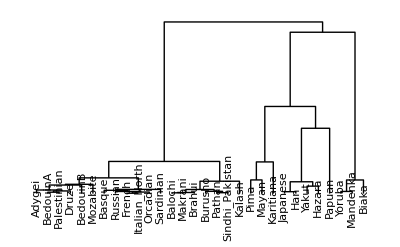

```mathematica
DendrogramPlot[clustering,LeafLabels->(Rotate[popList[[#]],Pi/2]&)]
```

```mathematica
leafOrder=clustering//ClusterFlatten
```

{1,4,22,9,5,20,3,26,10,13,21,27,2,17,7,8,24,28,15,25,19,16,14,11,29,12,23,30,18,6}

```mathematica
sortedFstMat=Table[
fstMat[[x,y]],
{x,leafOrder},{y,leafOrder}];
```

```mathematica
ticks=MapIndexed[{#2[[1]],#1}&,popList[[#]]&/@leafOrder];
ArrayPlot[sortedFstMat,FrameTicks->{{ticks,None},{None,{#[[1]],Rotate[#[[2]],Pi/2]}&/@ticks}},
PlotLegends->Automatic]
```

-Graphics-

## Comparison with smartPCA

```mathematica
smartPCAdatRaw=Import["FST_admixtools_Joscha.log","Table"];
```

```mathematica
smartPCApopNames=smartPCAdatRaw[[49;;78,1]]
```

{Pima,Mayan,Karitiana,Mandenka,French,Orcadian,Basque,Mozabite,Yoruba,Sardinian,Italian_North,Biaka,Russian,Druze,BedouinA,Palestinian,BedouinB,Adygei,Makrani,Balochi,Brahui,Sindhi_Pakistan,Hazara,Pathan,Kalash,Burusho,Han,Yakut,Japanese,Papuan}

```mathematica
Length@smartPCApopNames
```

30

```mathematica
spFSTmat=smartPCAdatRaw[[520;;549,2;;]];
```

```mathematica
Dimensions@spFSTmat
```

{30,30}

```mathematica
spFstDat=Dataset@Flatten[Table[
<|"popA"->smartPCApopNames[[i]],"popB"->smartPCApopNames[[j]],"fstSmartPCA"->spFSTmat[[i,j]]/1000000.|>,
{i,30},{j,30}],1];
```

```mathematica
joinedDat=JoinAcross[spFstDat,dat[Select[#Statistic=="FST"&],{"a","b","Estimate_Total"}],{"popA"->"a","popB"->"b"}]
```

xerxes produces negative estimates for diagonal entries. That’s fine for now.

```mathematica
plotDat=joinedDat[All,{#[["fstSmartPCA"]],#[["Estimate_Total"]]}&]//Normal;
```

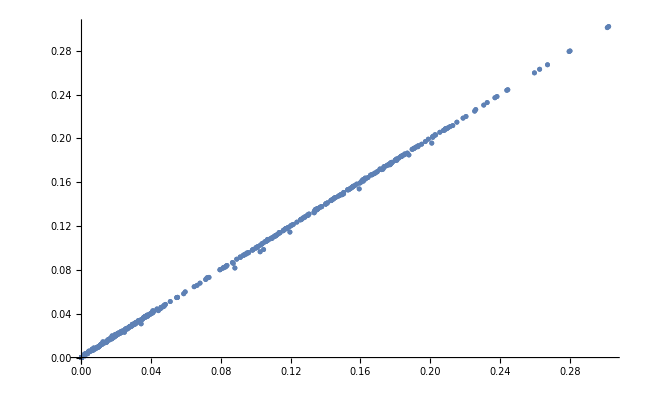

```mathematica
ListPlot[plotDat]
```